## Study of the deviation of a theoretical value from the experimental value

```mathematica
allowedValues[x0_,dev_,n_]:=Table[RandomReal[{x0,x0+RandomChoice[{-1,1}]*dev}],{i,1,n,1}];
rPlot[x0_,dev_,n_]:=ListPlot[allowedValues[x0,dev,n],Joined->True,Frame->True,Axes->False,Axes->False,PlotMarkers->{Automatic, Medium},PlotRange->Full]
```

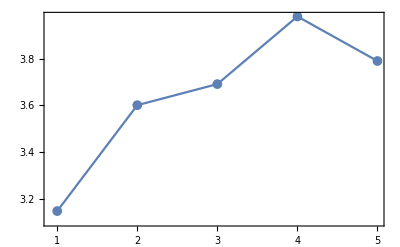

```mathematica
rPlot[3,1,5]
```

```mathematica
expDev[expvals_,thval_]:=Table[Abs[expvals[[i]]-thval]/expvals[[i]],{i,1,Length[expvals]}];
thDev[thvals_,expval_]:=Table[Abs[thvals[[i]]-expval]/thvals[[i]],{i,1,Length[thvals]}];
```

### Compute the relative error for a data set

```mathematica
relError[dataset_,expval_]:=Table[Abs[(dataset[[i]]-expval)]/expval,{i,1,Length[dataset]}];
```

```mathematica
p1=relError[allowedValues[3,0.2,10],3.5];
Print["ϵ= ",#*100," %"]&/@p1;
```

ϵ= 14.7197 %

ϵ= 17.1699 %

ϵ= 12.0037 %

ϵ= 11.5804 %

ϵ= 13.421 %

ϵ= 19.1233 %

ϵ= 18.5955 %

ϵ= 10.6567 %

ϵ= 14.8708 %

ϵ= 11.359 %